# Ordinary Differential Equations

## Geometrical View of ODEs

### Example 1

Consider the ODE y'=-x/y Its solution is given by:

```mathematica
DSolve[y'[x]==-x/y[x],y[x],x][[1,1]]/.C[1]->c
```

y[x]→-√(2 c-x^2)

```mathematica
DSolve[y'[x]==-x/y[x],y[x],x][[2,1]]/.C[1]->c
```

y[x]→√(2 c-x^2)

Now we draw the direction field and the integral curves. For a specific slope value c the isocline is given by -x/y=c → y=-x/c

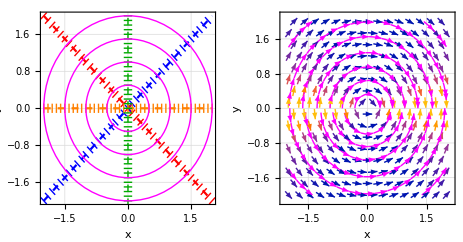

```mathematica
Isocline1=Plot[{-x/-1},{x,-2,2},PlotStyle->{Dashed,Blue},Frame->True,GridLines->Automatic,FrameLabel->{"x","y"},AspectRatio->1];
Isocline2=Plot[{-x/1},{x,-2,2},PlotStyle->{Dashed,Red}];
Isocline3=Plot[{-x/Infinity},{x,-2,2},PlotStyle->{Dashed,Orange}];
Isocline4=Graphics[{Dashed,Darker[Green],Line[{{0,-2.1},{0,2.1}}]}];
LineElement1=Graphics[{Blue,Line[Table[{{x-0.1/(√2),-x/-1+0.1/(√2)},{x+0.1/(√2),-x/-1-0.1/(√2)}},{x,-2,1.95,0.1}]]}];
LineElement2=Graphics[{Red,Line[Table[{{x-0.1/(√2),-x/1-0.1/(√2)},{x+0.1/(√2),-x/1+0.1/(√2)}},{x,-2,2,0.1}]]}];
LineElement3=Graphics[{Orange,Line[Table[{{x,-0.1},{x,0.1}},{x,-2,2,0.1}]]}];
LineElement4=Graphics[{Darker[Green],Line[Table[{{-0.1,y},{0.1,y}},{y,-2.1,2.1,0.1}]]}];
IntegraLCurve=Graphics[{Magenta,Circle[{0,0},0.5],Circle[{0,0},1],Circle[{0,0},1.5],Circle[{0,0},2]}];
DirectionFieldManual=Show[Isocline1,Isocline2,Isocline3,Isocline4,LineElement1,LineElement2,LineElement3,LineElement4,IntegraLCurve];
DirectionFieldComputer=VectorPlot[{1,-x/y},{x,-2,2},{y,-2,2},StreamPoints->Coarse,StreamColorFunction->None,StreamStyle->Magenta,FrameLabel->{"x","y"},GridLines->Automatic];
GraphicsGrid[{{DirectionFieldManual,DirectionFieldComputer}}]
```

### Example 1

Consider the ODE y'=1+x-y Its solution is given by:

```mathematica
DSolve[y'[x]==1+x-y[x],y[x],x][[1,1]]/.C[1]->c
```

y[x]→c ⅇ^-x+x

Now we draw the direction field and the integral curves. For a specific slope value c the isocline is given by 1+x-y=c → y=x+1-c

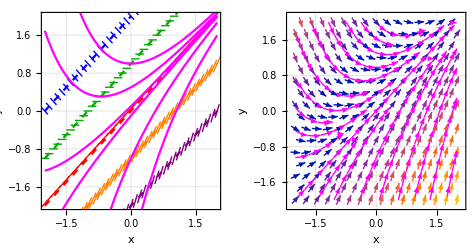

```mathematica
Isocline1=Plot[{x+2},{x,-2,2},PlotStyle->{Dashed,Blue},PlotRange->{{-2,2},{-2,2}},Frame->True,GridLines->Automatic,FrameLabel->{"x","y"},AspectRatio->1];
Isocline2=Plot[{x+1},{x,-2,2},PlotStyle->{Dashed,Darker[Green]}];
Isocline3=Plot[{x},{x,-2,2},PlotStyle->{Dashed,Red}];
Isocline4=Plot[{x-1},{x,-2,2},PlotStyle->{Dashed,Orange}];
Isocline5=Plot[{x-2},{x,-2,2},PlotStyle->{Dashed,Purple}];
LineElement1=Graphics[{Blue,Line[Table[{{x-0.1/(√2),x+2+0.1/(√2)},{x+0.1/(√2),x+2-0.1/(√2)}},{x,-2,1.95,0.1}]]}];
LineElement2=Graphics[{Darker[Green],Line[Table[{{x-0.1,x+1},{x+0.1,x+1}},{x,-2,1.95,0.1}]]}];
LineElement3=Graphics[{Red,Line[Table[{{x-0.1/(√2),x-0.1/(√2)+0.05},{x+0.1/(√2),x+0.1/(√2)+0.05}},{x,-2,2,0.1}]]}];
LineElement4=Graphics[{Orange,Line[Table[{{x-√(0.4^2/20),x-1-√(0.4^2/5)},{x+√(0.4^2/20),x-1+√(0.4^2/5)}},{x,-2,2,0.1}]]}];
LineElement5=Graphics[{Purple,Line[Table[{{x-√(0.3^2/40),x-2-3/2*√(0.3^2/10)},{x+√(0.3^2/40),x-2+3/2*√(0.3^2/10)}},{x,-2,2,0.1}]]}];
IntegraLCurve=Plot[{ⅇ^-x+x,0.5*ⅇ^-x+x,0.1*ⅇ^-x+x,-0.1*ⅇ^-x+x,-ⅇ^-x+x,-3 ⅇ^-x+x},{x,-2,2},PlotStyle->{Magenta}];;
DirectionFieldManual=Show[Isocline1,Isocline2,Isocline3,Isocline4,Isocline5,LineElement1,LineElement2,LineElement3,LineElement4,LineElement5,IntegraLCurve];
DirectionFieldComputer=VectorPlot[{1,1+x-y},{x,-2,2},{y,-2,2},StreamPoints->Coarse,StreamColorFunction->None,StreamStyle->Magenta,FrameLabel->{"x","y"},GridLines->Automatic];
GraphicsGrid[{{DirectionFieldManual,DirectionFieldComputer}}]
```